```mathematica
SetOptions[$FrontEnd,Magnification->1.5]
```

# p波

## 全局设定

```mathematica
Clear["Global`*"]
```

```mathematica
$Assumptions={g1∈Reals &&g2∈Reals && g12∈Reals  && g1>0 && g2>0 && g12<0 && n1∈Reals&& n2∈Reals  && n1>0&& n2>0&& g3>0};
```

## 写出κM的表达式

```mathematica
M={{A+g n+g3 A n,g n,n(g12-g3 A),n g12},{g n,A+g n+g3 A n,n g12,n(g12-g3 A)},{n(g12-g3 A),n g12,A+g n+g3 A n,g n},{n g12,n(g12-g3 A),g n,A+g n+g3 A n}}
```

{{A+g n+A g3 n,g n,(g12-A g3) n,g12 n},{g n,A+g n+A g3 n,g12 n,(g12-A g3) n},{(g12-A g3) n,g12 n,A+g n+A g3 n,g n},{g12 n,(g12-A g3) n,g n,A+g n+A g3 n}}

```mathematica
MatrixForm[M]
```

(A+g n+A g3 n | g n | (g12-A g3) n | g12 n
g n | A+g n+A g3 n | g12 n | (g12-A g3) n
(g12-A g3) n | g12 n | A+g n+A g3 n | g n
g12 n | (g12-A g3) n | g n | A+g n+A g3 n)

```mathematica
κ={{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}}
```

{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}}

```mathematica
MatrixForm[κ]
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
H1=Dot[κ,M]
```

{{A+g n+A g3 n,g n,(g12-A g3) n,g12 n},{-g n,-A-g n-A g3 n,-g12 n,-((g12-A g3) n)},{(g12-A g3) n,g12 n,A+g n+A g3 n,g n},{-g12 n,-((g12-A g3) n),-g n,-A-g n-A g3 n}}

```mathematica
MatrixForm[H1]
```

(A+g n+A g3 n | g n | (g12-A g3) n | g12 n
-g n | -A-g n-A g3 n | -g12 n | -((g12-A g3) n)
(g12-A g3) n | g12 n | A+g n+A g3 n | g n
-g12 n | -((g12-A g3) n) | -g n | -A-g n-A g3 n)

## 求 (Tr(κM))^2

```mathematica
H2=Dot[H1,H1]
```

{{-g^2 n^2-g12^2 n^2+(g12-A g3)^2 n^2+(A+g n+A g3 n)^2,g n (-A-g n-A g3 n)+g n (A+g n+A g3 n),-2 g g12 n^2+2 (g12-A g3) n (A+g n+A g3 n),g12 n (-A-g n-A g3 n)+g12 n (A+g n+A g3 n)},{-g n (-A-g n-A g3 n)-g n (A+g n+A g3 n),-g^2 n^2-g12^2 n^2+(g12-A g3)^2 n^2+(-A-g n-A g3 n)^2,-g12 n (-A-g n-A g3 n)-g12 n (A+g n+A g3 n),-2 g g12 n^2-2 (g12-A g3) n (-A-g n-A g3 n)},{-2 g g12 n^2+2 (g12-A g3) n (A+g n+A g3 n),g12 n (-A-g n-A g3 n)+g12 n (A+g n+A g3 n),-g^2 n^2-g12^2 n^2+(g12-A g3)^2 n^2+(A+g n+A g3 n)^2,g n (-A-g n-A g3 n)+g n (A+g n+A g3 n)},{-g12 n (-A-g n-A g3 n)-g12 n (A+g n+A g3 n),-2 g g12 n^2-2 (g12-A g3) n (-A-g n-A g3 n),-g n (-A-g n-A g3 n)-g n (A+g n+A g3 n),-g^2 n^2-g12^2 n^2+(g12-A g3)^2 n^2+(-A-g n-A g3 n)^2}}

```mathematica
FullSimplify[Tr[H2]/4]
```

A (A+2 (g+A g3) n+2 g3 (g-g12+A g3) n^2)

```mathematica
Expand[%8]
```

A^2+2 A g n+2 A^2 g3 n+2 A g g3 n^2-2 A g12 g3 n^2+2 A^2 g3^2 n^2

```mathematica
Coefficient[%10,A^2]
```

1+2 g3 n+2 g3^2 n^2

```mathematica
Coefficient[%10,A]
```

2 g n+2 g g3 n^2-2 g12 g3 n^2

## 求Det(κM)

```mathematica
FullSimplify[Det[H1]]
```

A^2 (A+2 (g+g12) n) (1+2 g3 n) (A+2 (g-g12+A g3) n)

```mathematica
Expand[(1+2C1(1+y))((2z+1)+2C1(1-y))(2z+1)]
```

1+4 C1+4 C1^2-4 C1^2 y^2+4 z+12 C1 z+8 C1^2 z+4 C1 y z-8 C1^2 y^2 z+4 z^2+8 C1 z^2+8 C1 y z^2

```mathematica
Coefficient[%160,C1^2]
```

4-4 y^2+8 z-8 y^2 z

## 激发谱图像

### 设定无量纲参数数值

```mathematica
y=0.2
```

0.2

### 激发谱上支

```mathematica
z=0.5;
ϵ=Table[√(k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2)+√((k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2))^2-(k^4/4(k^2/2+2(1+y))(k^2/2(2z+1)+2-2y)(2z+1)))),{k,0,3,0.001}];
ϵ00=Table[√(k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2)-√((k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2))^2-(k^4/4(k^2/2+2(1+y))(k^2/2(2z+1)+2-2y)(2z+1)))),{k,0,3,0.001}];
```

```mathematica
z=0;
ϵ1=Table[√(k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2)+√((k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2))^2-(k^4/4(k^2/2+2(1+y))(k^2/2(2z+1)+2-2y)(2z+1)))),{k,0,3,0.001}];
ϵ01=Table[√(k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2)-√((k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2))^2-(k^4/4(k^2/2+2(1+y))(k^2/2(2z+1)+2-2y)(2z+1)))),{k,0,3,0.001}];
```

```mathematica
z=1;
ϵ2=Table[√(k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2)+√((k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2))^2-(k^4/4(k^2/2+2(1+y))(k^2/2(2z+1)+2-2y)(2z+1)))),{k,0,3,0.001}];
ϵ02=Table[√(k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2)-√((k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2))^2-(k^4/4(k^2/2+2(1+y))(k^2/2(2z+1)+2-2y)(2z+1)))),{k,0,3,0.001}];
```

```mathematica
z=2;
ϵ3=Table[√(k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2)+√((k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2))^2-(k^4/4(k^2/2+2(1+y))(k^2/2(2z+1)+2-2y)(2z+1)))),{k,0,3,0.001}];
ϵ03=Table[√(k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2)-√((k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2))^2-(k^4/4(k^2/2+2(1+y))(k^2/2(2z+1)+2-2y)(2z+1)))),{k,0,3,0.001}];
```

```mathematica
z=0.1;
ϵ4=Table[√(k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2)+√((k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2))^2-(k^4/4(k^2/2+2(1+y))(k^2/2(2z+1)+2-2y)(2z+1)))),{k,0,3,0.001}];
ϵ04=Table[√(k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2)-√((k^4/4(2 z^2+2z+1)+k^2/2(2z-2y z+2))^2-(k^4/4(k^2/2+2(1+y))(k^2/2(2z+1)+2-2y)(2z+1)))),{k,0,3,0.001}];
```

```mathematica
a=Table[z1,{z1,0,3,0.001}];
```

```mathematica
spec={a,ϵ}//Transpose;
spec00={a,ϵ00}//Transpose;
spec1={a,ϵ1}//Transpose;
spec01={a,ϵ01}//Transpose;
spec2={a,ϵ2}//Transpose;
spec02={a,ϵ02}//Transpose;
spec3={a,ϵ3}//Transpose;
spec03={a,ϵ03}//Transpose;
spec4={a,ϵ4}//Transpose;
spec04={a,ϵ04}//Transpose;
```

```mathematica
g1f=ListLinePlot[spec,PlotStyle->{Darker[Orange],Dotted},PlotRange->All,Ticks->{{0,2,4},{0,2,4,6,8}},AspectRatio->0.8,LabelStyle->Directive[15],PlotMarkers->{"o",1.5},Frame->{{True,True},{True,True}},PlotLegends->LineLegend[{"z1=0.5"}]];
g1f00=ListLinePlot[spec00,PlotStyle->{Darker[Orange],Dotted},PlotMarkers->{"o",2},PlotRange->All,Ticks->{{0,2,4},{0,2,4,6,8}},AspectRatio->0.8,LabelStyle->Directive[15],Frame->{{True,True},{True,True}},PlotLegends->LineLegend[{"z1=0.5"}]];
g1f1=ListLinePlot[spec1,PlotStyle->{Black,Thickness[0.005]},PlotRange->All,Ticks->{{0,2,4},{0,2,4,6,8}},AspectRatio->0.8,LabelStyle->Directive[15],Frame->{{True,True},{True,True}},PlotLegends->LineLegend[{"z1=0"}]];
g1f01=ListLinePlot[spec01,PlotStyle->{Black,Thickness[0.005]},PlotRange->All,Ticks->{{0,2,4},{0,2,4,6,8}},AspectRatio->0.8,LabelStyle->Directive[15],Frame->{{True,True},{True,True}},PlotLegends->LineLegend[{"z1=0"}]];
g1f2=ListLinePlot[spec2,PlotStyle->{Darker[Green],Dashing[{0.02,0.02}]},PlotRange->All,Ticks->{{0,2,4},{0,2,4,6,8}},AspectRatio->0.7,LabelStyle->Directive[15],Frame->{{True,True},{True,True}},PlotLegends->LineLegend[{"z1=1"}]];
g1f02=ListLinePlot[spec02,PlotStyle->{Darker[Green],Dashing[{0.02,0.02}]},PlotRange->All,Ticks->{{0,2,4},{0,2,4,6,8}},AspectRatio->0.8,LabelStyle->Directive[15],Frame->{{True,True},{True,True}},PlotLegends->LineLegend[{"z1=1"}]];
g1f3=ListLinePlot[spec3,PlotStyle->{Blue,Dashing[{0.08,0.08}]},PlotRange->All,Ticks->{{0,2,4},{0,2,4,6,8}},AspectRatio->0.8,LabelStyle->Directive[15],Frame->{{True,True},{True,True}},PlotLegends->LineLegend[{"z1=2"}]];
g1f03=ListLinePlot[spec03,PlotStyle->{Blue,Dashing[{0.08,0.08}]},PlotRange->All,Ticks->{{0,2,4},{0,2,4,6,8}},AspectRatio->0.8,LabelStyle->Directive[15],Frame->{{True,True},{True,True}},PlotLegends->LineLegend[{"z1=2"}]];
g1f4=ListLinePlot[spec4,PlotStyle->{Red,Dashing[{0.004}]},PlotRange->All,Ticks->{{0,2,4},{0,2,4,6,8}},AspectRatio->0.8,LabelStyle->Directive[15],Frame->{{True,True},{True,True}},PlotLegends->LineLegend[{"z1=0.1"}]];
g1f04=ListLinePlot[spec04,PlotStyle->{Red,Dashing[{0.004}]},PlotRange->All,Ticks->{{0,2,4},{0,2,4,6,8}},AspectRatio->0.8,LabelStyle->Directive[15],Frame->{{True,True},{True,True}},PlotLegends->LineLegend[{"z1=0.1"}]];
```

```mathematica
spec
```

{{0.,0.},{0.001,0.00126491},{0.002,0.00252983},{0.003,0.00379474},{0.004,0.00505967},{0.005,0.0063246},{0.006,0.00758955},{0.007,0.00885451},{0.008,0.0101195},{0.009,0.0113845},2982,{2.992,9.7192},{2.993,9.7252},{2.994,9.73121},{2.995,9.73722},{2.996,9.74323},{2.997,9.74924},{2.998,9.75526},{2.999,9.76127},{3.,9.76729}}
 |  |  |  |

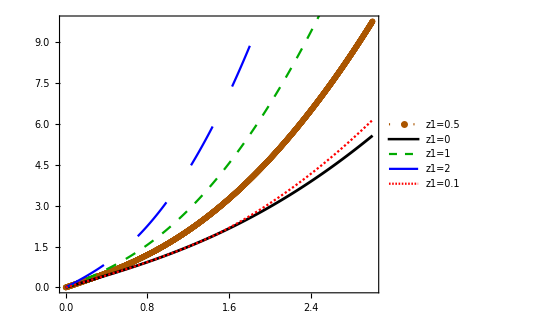

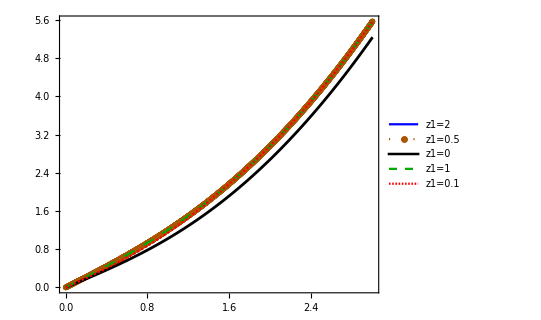

```mathematica
excip=Show[g1f,g1f1,g1f2,g1f3,g1f4]
excin=Show[g1f03,g1f00,g1f01,g1f02,g1f04]
```

```mathematica
Export["excip.eps",excip];
Export["excin.eps",excin];
```

## 能量图像

## 发散项

```mathematica
Coefficient[%160,C1^2]
```

4-4 y^2+8 z-8 y^2 z

```mathematica
Coefficient[%160,C1]
```

4+12 z+4 y z+8 z^2+8 y z^2

```mathematica
%160-Expand[%162*C1^2]-Expand[%163*C1]
```

1+4 z+4 z^2

```mathematica
Series[√((1+2z+2 z^2)+C1(2+2z-2y z)-√(((1+2z+2 z^2)+C1(2+2z-2y z))^2-(1+4z+4 z^2+2C1(2+6z+2y z+4 z^2+4y z^2)+C1^2(8z+4-4 y^2-8 y^2 z)))),{C1,0,2}]
```

1+((2+2 z-2 y z+(2 (y z-z^2+2 y z^2-z^3+y z^3))/(√(z^2 (1+z)^2))) C1)/(2 (1+2 z+2 z^2-2 √(z^2 (1+z)^2)))-((2+2 z-2 y z+(2 (y z-z^2+2 y z^2-z^3+y z^3))/(√(z^2 (1+z)^2)))^2 C1^2)/(8 (1+2 z+2 z^2-2 √(z^2 (1+z)^2))^2)+O[C1]^3

```mathematica
FullSimplify[1+((2+2 z-2 y z+(2 (y z-z^2+2 y z^2-z^3+y z^3))/(√(z^2 (1+z)^2))) C1)/(2 (1+2 z+2 z^2-2 √(z^2 (1+z)^2)))-((2+2 z-2 y z+(2 (y z-z^2+2 y z^2-z^3+y z^3))/(√(z^2 (1+z)^2)))^2 C1^2)/(8 (1+2 z+2 z^2-2 √(z^2 (1+z)^2))^2)]
```

1-1/2 C1 (1+y) (-2+C1+C1 y)

```mathematica
Expand[1-1/2 C1 (1+y) (-2+C1+C1 y)]
```

1+C1-C1^2/2+C1 y-C1^2 y-(C1^2 y^2)/2

```mathematica
Series[√((1+2z+2 z^2)+C1(2+2z-2y z)+√(((1+2z+2 z^2)+C1(2+2z-2y z))^2-(1+4z+4 z^2+2C1(2+6z+2y z+4 z^2+4y z^2)+C1^2(8z+4-4 y^2-8 y^2 z)))),{C1,0,2}]
```

√(1+4 z+4 z^2)-((-1+y) √((1+2 z)^2) C1)/(1+2 z)-((-1+y)^2 C1^2)/(2 √((1+2 z)^2))+O[C1]^3

```mathematica
FullSimplify[√(1+4 z+4 z^2)-((-1+y) √((1+2 z)^2) C1)/(1+2 z)-((-1+y)^2 C1^2)/(2 √((1+2 z)^2))]
```

(-C1^2 (-1+y)^2-2 C1 (-1+y) (1+2 z)+2 (1+2 z)^2)/(2+4 z)

```mathematica
$Assumptions={z>0&&y>0};
```

```mathematica
FullSimplify[%165+%166]
```

2 (1+z)+2 C1-((1+y^2+(1+y)^2 z) C1^2)/(1+2 z)+O[C1]^3

```mathematica
Clear["Global`*"]
```

```mathematica
y=0.2;
inte={};
```

```mathematica
Integrate[k^2(√(k^4/4(1+2z+2 z^2)+k^2/2(2+2z-2y z)+√((k^4/4(1+2z+2 z^2)+k^2/2(2+2z-2y z))^2-(k^4/4(k^2/2+2(1+y))(k^2/2(2z+1)+2-2y)(2z+1))))+√(k^4/4(1+2z+2 z^2)+k^2/2(2+2z-2y z)-√((k^4/4(1+2z+2 z^2)+k^2/2(2+2z-2y z))^2-(k^4/4(k^2/2+2(1+y))(k^2/2(2z+1)+2-2y)(2z+1))))-(k^2(z+1)+2-(y^2+(y+1)^2 z+1)/((2z+1)(k^2/2)))),{k,0,∞}]
```

ConditionalExpression[1/(15+30 z)32 (√(1+y)+2 √(1+y) z+√((1-y)/(1+2 z))+2 y (√(1+y)+2 √(1+y) z-√((1-y)/(1+2 z)))+y^2 (√(1+y)+2 √(1+y) z+√((1-y)/(1+2 z)))), y+y z<z]

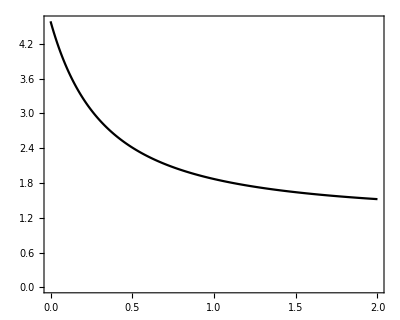

```mathematica
f[y_,z_]:=(1/(15+30 z))*32*(Sqrt[1+y]+2 Sqrt[1+y] z+Sqrt[(1-y)/(1+2 z)]+2 y (Sqrt[1+y]+2 Sqrt[1+y] z-Sqrt[(1-y)/(1+2 z)])+y^2 (Sqrt[1+y]+2 Sqrt[1+y] z+Sqrt[(1-y)/(1+2 z)]))

(*生成表格数据*)
data=Table[{z,f[-0.2,z]},{z,0,2,0.01}];
(*绘制图像*)
ene=ListLinePlot[data,PlotStyle->{Black},PlotRange->All,Ticks->{{0,2,4},{0,2,4,6,8}},AspectRatio->0.8,LabelStyle->Directive[15],Frame->{{True,True},{True,True}},PlotLegends->LineLegend[{}]]
```

```mathematica
Export["energy.eps",ene]
```

energy.eps